```mathematica
SetDirectory@If[$FrontEnd===Null,DirectoryName[$InputFileName],NotebookDirectory[]]
```

\\wsl.localhost\Ubuntu\home\fytc\workspace\FAD-sym

```mathematica
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

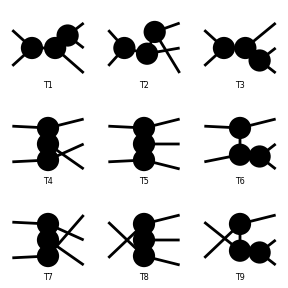

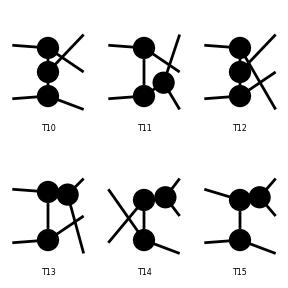

```mathematica
topo23=CreateTopologies[0,2->3,Adjacencies->3];
Paint[topo23];
```

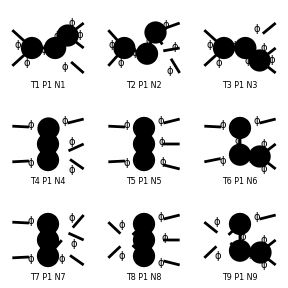

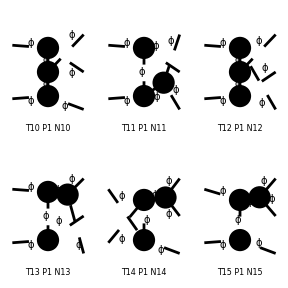

```mathematica
diag23=InsertFields[topo23,{S[1],S[1]}->{S[1],S[1],S[1]},InsertionLevel->{Particles},Model -> FileNameJoin[{"Phi3","Phi3"}],GenericModel-> FileNameJoin[{"Phi3","Phi3"}]];
Paint[diag23];
```

```mathematica
iM23=FCFAConvert[
CreateFeynAmp[diag23,Truncated->True,GaugeRules->{},PreFactor->1],
IncomingMomenta->{pa,pb},OutgoingMomenta->{k1,k2,k3},
LorentzIndexNames->{},LoopMomenta->{},UndoChiralSplittings->True,ChangeDimension->D,List->True,SMP->True,
FinalSubstitutions->{GaugeXi@S[1]->1,Mphi->m}
];
M23Sqr=FAD[{k1,m},{k2,m},{k3,m}]Total[iM23] ComplexConjugate@Total[iM23]/.k3->pa+pb-k1-k2//Expand;
M23Sqr=FCE@ApartFF[M23Sqr,{k1,k2}];
(*M23Sqr=M23Sqr//.{
k3->pa+pb-k1-k2,

FAD[{-k1-k2,m},term___]->FAD[{k1+k2,m},term],
FAD[{-k1-k2+pa,m},term___]->FAD[{k1+k2-pa,m},term],
FAD[{-k1-k2+pb,m},term___]->FAD[{k1+k2-pb,m},term],

FAD[{-k1+pa,m},term___]->FAD[{k1-pa,m},term],
FAD[{-k1+pb,m},term___]->FAD[{k1-pb,m},term],
FAD[{-k1+pa+pb,m},term___]->FAD[{k1-pa-pb,m},term],

FAD[{-k2+pa,m},term___]->FAD[{k2-pa,m},term],
FAD[{-k2+pb,m},term___]->FAD[{k2-pb,m},term],
FAD[{-k2+pa+pb,m},term___]->FAD[{k2-pa-pb,m},term],

FAD[{-pa-pb,m},term___]->y,
FAD[{pa+pb,m},term___]->y
}//Expand;*)
momList={{k1,1},{k2,2},{k1+k2-pa-pb,3},{k1+k2,4},{k1+k2-pa,5},{k1+k2-pb,6},{k1-pa,7},{k1-pb,8},{k1-pa-pb,9},{k2-pa,10},{k2-pb,11},{k2-pa-pb,12}};
ruleFAD=Flatten[{
{pa+pb,_}->1/(s-m^2),
SPD[pa,pb]->(s-2 m^2)/2,
Table[{mom[[1]],_}->x[mom[[2]]],{mom,momList}],
FAD->Times
}];
M23Sqr=M23Sqr/.ruleFAD
```

(x(1) x(2) x(3) (x(4))^2 g^6)/((s-m^2)^2)+x(1) x(2) x(3) (x(4))^2 (x(5))^2 g^6+x(1) x(2) x(3) (x(4))^2 (x(6))^2 g^6+x(1) x(2) x(3) (x(5))^2 (x(7))^2 g^6+x(1) x(2) x(3) (x(6))^2 (x(8))^2 g^6+x(1) x(2) x(3) (x(7))^2 (x(9))^2 g^6+x(1) x(2) x(3) (x(8))^2 (x(9))^2 g^6+(x(1) x(2) x(3) (x(9))^2 g^6)/((s-m^2)^2)-(4 x(1) x(2) x(3) x(7) (x(9))^2 g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) x(7) (x(9))^2 g^6)/(s-m^2)-(4 x(1) x(2) x(3) x(8) (x(9))^2 g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) x(8) (x(9))^2 g^6)/(s-m^2)+x(1) x(2) x(3) (x(5))^2 (x(10))^2 g^6+x(1) x(2) x(3) (x(8))^2 (x(10))^2 g^6+2 x(1) x(2) x(3) x(5) x(8) (x(10))^2 g^6+x(1) x(2) x(3) (x(6))^2 (x(11))^2 g^6+x(1) x(2) x(3) (x(7))^2 (x(11))^2 g^6+2 x(1) x(2) x(3) x(6) x(7) (x(11))^2 g^6+x(1) x(2) x(3) (x(10))^2 (x(12))^2 g^6+x(1) x(2) x(3) (x(11))^2 (x(12))^2 g^6+(x(1) x(2) x(3) (x(12))^2 g^6)/((s-m^2)^2)+(2 x(1) x(2) x(3) x(10) (x(12))^2 g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(11) (x(12))^2 g^6)/(s-m^2)+(4 x(1) x(3) x(10) x(11) (x(12))^2 g^6)/(s-2 m^2)-(2 x(1) x(2) x(3) (x(4))^2 x(5) g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) (x(4))^2 x(5) g^6)/(s-m^2)-(2 x(1) x(2) x(3) x(4) x(5) g^6)/((s-2 m^2)^2)-(2 x(1) x(2) x(3) (x(4))^2 x(6) g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) (x(4))^2 x(6) g^6)/(s-m^2)-(2 x(1) x(2) x(3) x(4) x(6) g^6)/((s-2 m^2)^2)+(2 x(1) x(2) (x(4))^2 x(5) x(6) g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) x(5) x(6) g^6)/((s-2 m^2)^2)+(2 x(1) x(2) x(4) x(5) x(6) g^6)/((s-2 m^2)^2)+2 x(1) x(2) x(3) x(4) (x(5))^2 x(7) g^6-(4 x(1) x(2) x(3) x(4) x(5) x(7) g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) x(4) x(5) x(7) g^6)/(s-m^2)-(4 x(1) x(2) x(3) x(4) x(6) x(7) g^6)/(s-2 m^2)+(4 x(1) x(2) x(3) x(5) x(6) x(7) g^6)/(s-2 m^2)+(4 x(1) x(2) x(4) x(5) x(6) x(7) g^6)/(s-2 m^2)+2 x(1) x(2) x(3) x(4) (x(6))^2 x(8) g^6-(4 x(1) x(2) x(3) x(4) x(5) x(8) g^6)/(s-2 m^2)-(4 x(1) x(2) x(3) x(4) x(6) x(8) g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) x(4) x(6) x(8) g^6)/(s-m^2)+(4 x(1) x(2) x(3) x(5) x(6) x(8) g^6)/(s-2 m^2)+(4 x(1) x(2) x(4) x(5) x(6) x(8) g^6)/(s-2 m^2)+(4 x(1) x(2) x(3) x(7) x(8) g^6)/((s-2 m^2)^2)+(4 x(1) x(2) x(3) x(5) x(7) x(8) g^6)/(s-2 m^2)+(4 x(1) x(2) x(3) x(6) x(7) x(8) g^6)/(s-2 m^2)+2 x(1) x(2) x(3) x(5) x(6) x(7) x(8) g^6+2 x(1) x(2) x(3) x(5) (x(7))^2 x(9) g^6+2 x(1) x(2) x(3) x(6) (x(8))^2 x(9) g^6+(2 x(1) x(2) x(3) x(4) x(9) g^6)/((s-m^2)^2)+(2 x(1) x(2) x(3) x(4) x(5) x(9) g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(4) x(6) x(9) g^6)/(s-m^2)-(4 x(1) x(2) x(3) x(7) x(9) g^6)/((s-2 m^2)^2)+(2 x(1) x(2) x(3) x(4) x(7) x(9) g^6)/(s-m^2)-(4 x(1) x(2) x(3) x(5) x(7) x(9) g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) x(5) x(7) x(9) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(4) x(5) x(7) x(9) g^6-(4 x(1) x(2) x(3) x(6) x(7) x(9) g^6)/(s-2 m^2)+2 x(1) x(2) x(3) x(4) x(6) x(7) x(9) g^6-(4 x(1) x(2) x(3) x(8) x(9) g^6)/((s-2 m^2)^2)+(2 x(1) x(2) x(3) x(4) x(8) x(9) g^6)/(s-m^2)-(4 x(1) x(2) x(3) x(5) x(8) x(9) g^6)/(s-2 m^2)+2 x(1) x(2) x(3) x(4) x(5) x(8) x(9) g^6-(4 x(1) x(2) x(3) x(6) x(8) x(9) g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) x(6) x(8) x(9) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(4) x(6) x(8) x(9) g^6+2 x(1) x(2) x(3) x(4) (x(5))^2 x(10) g^6+2 x(1) x(2) x(3) x(6) (x(8))^2 x(10) g^6+(2 x(1) x(2) x(3) x(4) x(5) x(10) g^6)/(s-m^2)+2 x(1) x(2) x(3) (x(5))^2 x(7) x(10) g^6+(2 x(1) x(2) x(3) x(4) x(8) x(10) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(4) x(5) x(8) x(10) g^6+2 x(1) x(2) x(3) x(4) x(6) x(8) x(10) g^6+2 x(1) x(2) x(3) x(5) x(6) x(8) x(10) g^6+(4 x(1) x(2) x(3) x(7) x(8) x(10) g^6)/(s-2 m^2)+2 x(1) x(2) x(3) x(5) x(7) x(8) x(10) g^6+2 x(1) x(2) x(3) (x(8))^2 x(9) x(10) g^6+(2 x(1) x(2) x(3) x(5) x(9) x(10) g^6)/(s-m^2)-(4 x(1) x(2) x(3) x(7) x(9) x(10) g^6)/(s-2 m^2)+2 x(1) x(2) x(3) x(5) x(7) x(9) x(10) g^6+(2 x(1) x(2) x(3) x(8) x(9) x(10) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(5) x(8) x(9) x(10) g^6+2 x(1) x(2) x(3) x(4) (x(6))^2 x(11) g^6+2 x(1) x(2) x(3) x(5) (x(7))^2 x(11) g^6+(2 x(1) x(2) x(3) x(4) x(6) x(11) g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(4) x(7) x(11) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(4) x(5) x(7) x(11) g^6+2 x(1) x(2) x(3) x(4) x(6) x(7) x(11) g^6+2 x(1) x(2) x(3) x(5) x(6) x(7) x(11) g^6+2 x(1) x(2) x(3) (x(6))^2 x(8) x(11) g^6+(4 x(1) x(2) x(3) x(7) x(8) x(11) g^6)/(s-2 m^2)+2 x(1) x(2) x(3) x(6) x(7) x(8) x(11) g^6+2 x(1) x(2) x(3) (x(7))^2 x(9) x(11) g^6+(2 x(1) x(2) x(3) x(6) x(9) x(11) g^6)/(s-m^2)-(4 x(1) x(2) x(3) x(7) x(9) x(11) g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) x(7) x(9) x(11) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(6) x(7) x(9) x(11) g^6-(4 x(1) x(2) x(3) x(8) x(9) x(11) g^6)/(s-2 m^2)+2 x(1) x(2) x(3) x(6) x(8) x(9) x(11) g^6+2 x(1) x(2) x(3) x(5) x(6) x(10) x(11) g^6+2 x(1) x(2) x(3) x(5) x(7) x(10) x(11) g^6+2 x(1) x(2) x(3) x(6) x(8) x(10) x(11) g^6+2 x(1) x(2) x(3) x(7) x(8) x(10) x(11) g^6+2 x(1) x(2) x(3) x(5) (x(10))^2 x(12) g^6+2 x(1) x(2) x(3) x(8) (x(10))^2 x(12) g^6+2 x(1) x(2) x(3) x(6) (x(11))^2 x(12) g^6+2 x(1) x(2) x(3) x(7) (x(11))^2 x(12) g^6+(2 x(1) x(2) x(3) x(4) x(12) g^6)/((s-m^2)^2)+(2 x(1) x(2) x(3) x(4) x(5) x(12) g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(4) x(6) x(12) g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(5) x(7) x(12) g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(6) x(8) x(12) g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(9) x(12) g^6)/((s-m^2)^2)+(2 x(1) x(2) x(3) x(7) x(9) x(12) g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(8) x(9) x(12) g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(4) x(10) x(12) g^6)/(s-m^2)+(2 x(1) x(2) x(3) x(5) x(10) x(12) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(4) x(5) x(10) x(12) g^6+2 x(1) x(2) x(3) x(4) x(6) x(10) x(12) g^6+2 x(1) x(2) x(3) x(5) x(7) x(10) x(12) g^6+(2 x(1) x(2) x(3) x(8) x(10) x(12) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(6) x(8) x(10) x(12) g^6+(2 x(1) x(2) x(3) x(9) x(10) x(12) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(7) x(9) x(10) x(12) g^6+2 x(1) x(2) x(3) x(8) x(9) x(10) x(12) g^6+(2 x(1) x(2) x(3) x(4) x(11) x(12) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(4) x(5) x(11) x(12) g^6+(2 x(1) x(2) x(3) x(6) x(11) x(12) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(4) x(6) x(11) x(12) g^6-(4 x(1) x(2) x(3) x(7) x(11) x(12) g^6)/(s-2 m^2)+(2 x(1) x(2) x(3) x(7) x(11) x(12) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(5) x(7) x(11) x(12) g^6+2 x(1) x(2) x(3) x(6) x(8) x(11) x(12) g^6+(2 x(1) x(2) x(3) x(9) x(11) x(12) g^6)/(s-m^2)+2 x(1) x(2) x(3) x(7) x(9) x(11) x(12) g^6+2 x(1) x(2) x(3) x(8) x(9) x(11) x(12) g^6+(4 x(1) x(3) x(10) x(11) x(12) g^6)/((s-2 m^2)^2)+(4 x(1) x(3) x(5) x(10) x(11) x(12) g^6)/(s-2 m^2)+(4 x(1) x(3) x(6) x(10) x(11) x(12) g^6)/(s-2 m^2)+(4 x(1) x(3) x(7) x(10) x(11) x(12) g^6)/(s-2 m^2)+(4 x(1) x(3) x(8) x(10) x(11) x(12) g^6)/(s-2 m^2)

```mathematica
M23SqrList=List@@Expand[M23Sqr];
exponentMat=Table[Exponent[term,x[ii]],{term,M23SqrList},{ii,1,12}];
coefficientList=M23SqrList/Table[Apply[Times,Table[x[ii],{ii,1,12}]^exponentList],{exponentList,exponentMat}];
```

```mathematica
denMomList=Table[First[mom],{mom,momList}];
Export["denMom.dat",denMomList];
Export["exponentMat.dat",exponentMat];
Export["coefficientList.dat",coefficientList];
```